# Computational Essays

## A Computational Essay on Computational Essays, Computational Languages, Computational Literacy, and Computational Thinking

Ethan Bogle

Stanford University Online High School

## Computational Essays and Computational Languages

This is an essay. It is what is called a Computational Essay. Why is it called a Computational Essay? Why am I capitalizing those words?

At a basic level, a Computational Essay is an essay composed of both 1) natural language text and 2) code that you can run in real time.

```mathematica
(*Whenever you see code, click it its cell and press ⇧+⌤ to evaluate it. You can identify code by a change in font and the fact that any code input cell will be preceded by In[#] in the left margin. This is code. ⇧+⌤*) 
Capitalize["computational essay","AllWords"]
```

A Computational Essay is an essay that harnesses a new type of evidence to prove its thesis. This evidence is computation.

Get the operating system this code is being run on:

```mathematica
(*This is code. ⇧+⌤*)
 $System
```

Get the version of the Wolfram Language this document is being run in:

```mathematica
(*This is more code. ⇧+⌤*)
$Version
```

In harnessing a new type of evidence, a Computational Essay is actually the natural historical “next step” of the evolution of essays and essay languages.

Let me explain what I mean by “essay languages”. Mathematical essays became much more communicative when they started incorporating symbolic mathematical language, a set of strange symbols that, while ineffective at communicating most things, are much more effective than natural language at articulating and communicating mathematical concepts. Try explaining this in natural language (this looks different, but it is also code, so you can use ⇧+⌤--you may see a popup warning when you run the more mathy-looking of these two cells, but you can go ahead with the evaluation):

```mathematica
∫1/(√(2 sin^2(x)))ⅆx==-(sin(x) (log(cos(x/2))-log(sin(x/2))))/(√(1-cos(2 x)))
```

```mathematica
SpokenString[Unevaluated[∫1/(√(2 Sin[x]^2))ⅆx==-(Sin[x] (Log[Cos[x/2]]-Log[Sin[x/2]]))/(√(1-Cos[2 x]))]]
```

Now give this equation to a third grader who doesn’t know calculus and ask them to verify it. They can, because this is just a piece of code. All they need to do is run it by moving the cursor to the cells with the equations in them and pressing ⇧+⌤; even though those cells don’t look like code, they actually are. The fact that you only have to run the code to verify these expressions is one of the key features of Computational Essays. But let me first continue talking about languages.

Without the language of equations, it is difficult to describe those mathematical concepts. Because it uses a foreign syntax and set of symbols, mathematics (and STEM in general) is probably the most obvious example of how the advent of a new, specialized language improved communication within a discipline. However, non-STEM disciplines have their own languages too. These specialized languages just look a lot more like natural language since they don’t use fancy symbols. They consist of a specialized vocabulary, applied in specialized ways, where everyone has practiced specialized ways of thinking. We teach students to write essays using this specialized language, and we teach students the relations between these pieces of language. In studying philosophy, we learn what terms like “social contract”, “induction”, “straw man”, and “social welfare” mean.

Get the dictionary definitions of these terms, and display them in a column with frames to make them easier to read:

```mathematica
AssociationMap[WordDefinition,{"social contract","induction","straw man","social welfare"}]//Normal//Column[#,Frame->All]&
```

Make a WordCloud of the contents of the philosopher Thomas Hobbes’s social contract theory book Leviathan. This code takes a few seconds to run since Leviathan is a very long work. It retrieves the contents of the text resource from the Wolfram Data Repository, counts the number of each word in it, and displays them with more common words displaying larger, fitting the words around each other so they don’t overlap. All this is done with one line of code:

```mathematica
ResourceData["Leviathan"]//WordCloud
```

When we teach languages (of the type that are written or spoken, like Spanish, Arabic, or Latin), we even develop special terms for different grammatical blocks, e.g. “part of speech”, “tense”, or even something as basic as “sentence”.

```mathematica
TextStructure["When we teach languages, we even develop special terms for different grammatical blocks."]
```

In art, we learn about the different types of effects that one can achieve with “colors”, “lines”, and “contrast”, and just as with natural language, we learn to understand “style”.

Get an image of Vincent van Gogh’s Starry Night:

```mathematica
LinguisticAssistant["Image"]
```

Get the dominant colors:

```mathematica
LinguisticAssistant["Image"]//DominantColors
```

Get the edges:

```mathematica
Entity["Artwork","TheStarryNight::VincentVanGogh"]["Image"]//EdgeDetect
```

Restyle an image of the Stanford University Campus like Starry Night (this computation takes 15-20 seconds, so you can keep reading while it finishes):

```mathematica
ImageRestyle[-Graphics-,-Graphics-]
```

Why do we teach students these specialized languages?

The rationale is simple: Evidence is not persuasive to us unless we can actually understand it. We humans have found that we need specialized languages to communicate the evidence needed to prove a thesis in our subject. Without these specialized languages, our messages are convoluted because natural language simply can’t express what we want to communicate at the level of precision that we customarily demand when presented with, as we call it, a thesis.

A Computational Essay introduces yet another new language to our existing library, one that was not accessible before. That language is a Computational Language. And just as we become literate in philosophical and mathematical languages, gaining Philosophical Literacy and Mathematical Literacy, when we learn a Computational Language, we gain Computational Literacy.

But wait, I just made it sound like I’m asking you to learn yet another set of mathematical symbols and words, or yet another set of philosophy lingo. The thing is, I’m not. This is because a Computational Language is different from other languages (even from programming languages, as I will explain).

The difference lies in the nature of the communicators.

A Computational Language fuses the natural language character of English or philosophy language, the precise character of symbolic math language, and the computer-interpretability of a programming language.

If that sounds like a lot of work, you're right--the Wolfram Language, arguably the only real Computational Language in existence, took over 30 years of heavily organized development to get where it is now.

WolframAlphaQueryResults

## Languages and Communicators

### One-Way Communications and Humans as Communicators

When you use a language, you use it to communicate. With whom? The purpose of natural language is to facilitate communication between two humans. Even if the natural language is no longer spoken (Salvē, Linguam Latinam loquentēs!), you use it to enable (one-way) communication from old dead guys to yourself.

```mathematica
Labeled[LinguisticAssistant["Image"],"Old Dead Guy"]
```

```mathematica
Entity["Person","Cicero::w5cz2"]["DeathDate"]
```

Graph this one-way communication (using ⇧+⌤):

```mathematica
Graph[{"You","Other Person"},{"Other Person"->"You"},VertexLabels->"Name"]
```

What about academic languages in the context of an essay? For most academic languages at this point in time, the communication is one-way from an author to a reader. An author writes mathematical notation or historical event names in an essay to communicate mathematical ideas or the relationship between historical events to a reader.

There’s one main academic language that tries to break this mold, but turns out to be pretty similar. This is programming languages. They seem to break this mold because, hey, isn’t the purpose of a programming language to communicate with a computer? In other words, isn’t the purpose of a programming language to allow an author to send information to a computer that a computer can understand?

But this gets the context wrong. Yes, a programming language is a communication device between humans and computers, but human authors write essays to communicate to other humans, not to computers. In an essay containing programming language code, the programming language code allows the author to tell the reader what to tell a computer to get it to rederive the results. This still helps communicate evidence--the human reader just requires extra computational help to verify the evidence (after they’ve used their own brain to check that the code actually works, which requires competency in the programming language)--but the communication is still fundamentally one-way.

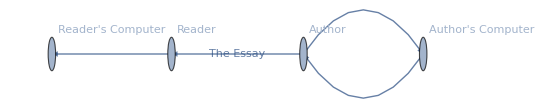

```mathematica
Graph[
{"Reader","Author","Reader's Computer","Author's Computer"},
{Labeled["Author"->"Reader","The Essay"],"Author"->"Author's Computer","Author's Computer"->"Author","Reader"->"Reader's Computer"},]
```

A Computational Essay, changes this pattern, however. This is because there are not two, but three parties to any communication that takes place in the Computational Language in a Computational Essay, and one of those communication pathways is two-way.

(Notice that I have folded up the cell with the graph in it so that only the output cell, with nice graphics, is visible. You can still see the code behind it by uncollapsing the cell, but this is a detail of the notebook interface that I don’t time to explain fully here, and that wouldn’t be very helpful right now. You have to double-click on the second cell bracket from the left to expand. To collapse it again, you have to double-click on the leftmost cell bracket of the output cell.)

### Two-Way Communications and Computers as Communicators

This is what the communication network around a Computational Essay looks like.

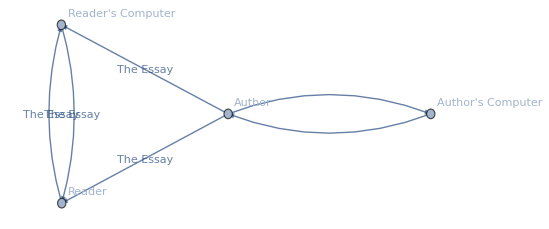

```mathematica
Graph[
{"Reader","Author","Reader's Computer","Author's Computer"},
{Labeled["Author"->"Reader","The Essay"],"Author"->"Author's Computer","Author's Computer"->"Author",Labeled["Reader"->"Reader's Computer","The Essay"],Labeled["Reader's Computer"->"Reader","The Essay"],Labeled["Author"->"Reader's Computer","The Essay"]},]
```

This gets down, finally, to the point of a Computational Essay and a Computational Language. Focus on the triangular relationship that takes place within the essay.

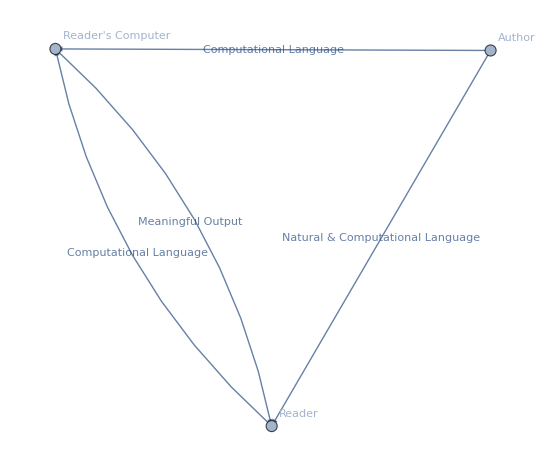

```mathematica
Graph[
{"Reader","Author","Reader's Computer"},
{Labeled["Author"->"Reader","Natural & Computational Language"],Labeled["Reader"->"Reader's Computer","Computational Language"],Labeled["Reader's Computer"->"Reader","Meaningful Output"],Labeled["Author"->"Reader's Computer","Computational Language"]},]
```

The Author communicates with both you and your computer. However, you and your computer have a two-way communication pathway with each other. This is what makes Computational Languages and Computational Essays uniquely powerful.

This communications triangle has two powerful implications.

The two-way communication between the reader and their computer enables the reader to explore the content of the essay, varying the existing code or writing their own to explore and test different ideas. The reader can not only verify what the author has said (by simply running the code themselves), but can also explore ideas that the author did not. The Computational Language, interpreted by the computer, allows the author to create interactive demonstrations and outputs that convey far more to a reader than a frozen graphic.

The reader does not have to be Computationally Literate to understand the Computational Language. Any Computational Language written by the author is interpreted by the reader’s computer into output that the reader can understand. The reader can use the computer to verify the author’s communications in the Computational Language without understanding the language. This means that any Computationally Literate author can write to any reader about any subject regardless of whether the reader is Computationally Literate. This is unlike (as far as I am aware) all other specialized academic languages. In any other language, a reader must be literate to understand anything.

## Computational Language and Computational Thinking

I’ve just discussed the idea of specialized academic languages in essays and compared that with Computational Languages in Computational Essays. Hopefully I’ve convinced you of the power of Computational Essays as a communication tool.

Part of the power of Computational Essays is that, since the Computational Language can be “translated” by the combined efforts of the author and the computer, the Computational Language can be “read” even if the reader is not Computationally Literate. However, to write Computational Essays still requires Computational Literacy. If I’ve been successful in convincing you that Computational Essays are powerful for readers, then it follows that we should teach students to write Computational Essays. Writing Computational Essays requires Computational Literacy, and Computational Literacy requires learning a Computational Language.

This is where Computational Thinking comes in. As I mentioned, when we learn specialized languages, we learn not only vocabulary and syntax, but also ways of thinking. When you learn Latin, that way of thinking involves breaking words into prefix-stem-ending format, interpreting the components separately, and discarding strict word order (as in English) for loose phrasal scoping. When you learn philosophy, that way of thinking involves always questioning every claim given with the goal of establishing, refuting, or refining. Learning a Computational Language requires learning “Computational Thinking”. So what does that mean? A Computational Language is designed to facilitate communication between humans and computers. The definition of Computational Thinking follows naturally from this:

Computational Thinking is the process of conceptualizing ideas in a way that a computer can understand.

Computers are powerful at the things they “understand”, and computers understand some things more easily than others. Originally, all they understood was numerical calculations. Gradually, however, humans have developed them to understand our world, including constructs like cities, people, faces, and speech. An expanding Computational Language reflects the increasing number of ideas that computers can understand, and humans have been able to design many products that translate a lot of human language into computational language for us (a chief example being Wolfram|Alpha). One can perhaps see the entire history of computer software and hardware development as humans’ progressive quest to build translators. But since most pieces of software only do specific things, few of these “translators” have tried to translate more than narrowly defined subsets of human language.

Of course, some ideas can be understood by computers much more easily than others simply because of the way they are built. Numerical arithmetic, for example, is one of the fundamental operations that computers perform, so we expect computers to be good at that, but I would be interested to know if computers will ever be able to “think” about the very human question “what is the meaning of life”. On the other hand, humans will probably never be able to really comprehend the graph of the internet or what is happening inside a neural network--something that computers may struggle at for now, but will probably eventually achieve.

But lest I get sidetracked by a philosophical discussion of understanding, let me reiterate the important idea: Computational Thinking views computers as a powerful tool for exploring and solving human problems, and is the way of thinking necessary to learn and use a Computational Language to communicate with them.

## Conclusion

I’ve thrown around a lot of terms in this Computational Essay. It would be bad enough if they were technical terms that had complicated definitions, but the actuality is worse: as of this writing, many of these terms are in their infancy, and people still disagree on the meaning of many of them and the best way to characterize their meanings.

So what I’m going to do here is reiterate the definitions that I gave of these terms:

A Computational Essay is an essay that harnesses a new type of evidence to prove its thesis. This evidence is computation.

A Computational Language fuses the natural language character of English or philosophy language, the precise character of symbolic math language, and the computer-interpretability of a programming language.

Computational Thinking is the process of conceptualizing ideas in a way that a computer can understand.

And one more term that I haven’t yet given a definition for:

Computational Literacy is the ability to use Computational Thinking to read and write Computational Language, for example reading and writing Computational Essays.

Computational Essays are powerful because they allow for a two-way communication pathway between the reader and their computer, and can be read even by those who are not Computationally Literate. We need to teach students to write Computational Essays, which requires teaching them a Computational Language, which involves teaching them the way of thinking associated with Computational Languages, namely Computational Thinking.

## Acknowledgements and Attributions

This essay was written while attending the 2019 Wolfram Summer School.

Thank you to Kyle Keane, Katja Della Libera, and Daavid Väänänen for taking the time to review drafts of this essay. Thank you to to Kyle Keane, Danielle Rommel, and Jonathan Gorard for contributing several ideas that I did not end up fitting into this essay, but nevertheless helped me in my thinking process. Thank you also to Daavid Väänänen and the other students in the Educational Innovation Track at the 2019 Wolfram Summer School for their valuable insights.

Thank you to my parents for being interested in this and reading and giving feedback on my drafts.